Sin[x]/x

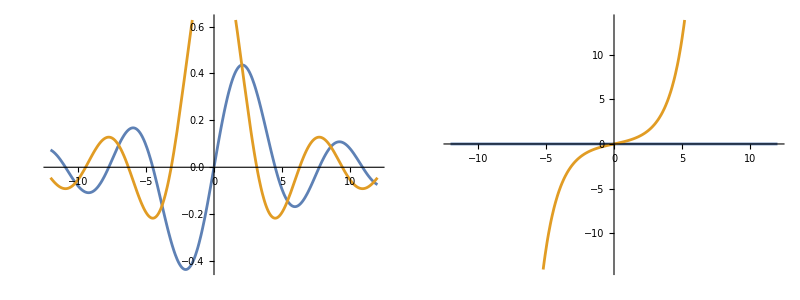

```mathematica
SphericalBesselJ[0,x]//FunctionExpand
Grid[{{Plot[{Re[SphericalBesselJ[1,x]],Re[SphericalBesselJ[0,x]]},{x,-12,12},ImageSize->Large],Plot[{Im[SphericalBesselJ[1,x]],Im[SphericalBesselJ[1,I x]]},{x,-12,12},ImageSize->Large]}}]
```